# Measurement results visualization

Visualize measurement results

## Example Content

Quantum measurement results can be obtained exactly in Wolfram quantum framework. The information about measurement is saved in a non-destructive way, by incorporating classical qudits.

Install and load the QuantumFramework paclet:

```mathematica
PacletInstall["Wolfram/QuantumFramework"]
Needs["Wolfram`QuantumFramework`"]
```

Plot measurement probabilities for measuring a qubit in computational basis:

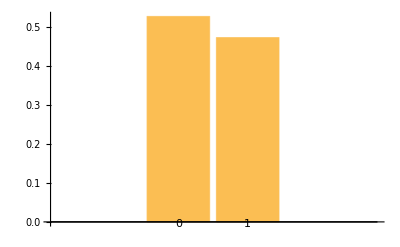

```mathematica
QuantumMeasurementOperator[][QuantumState["RandomPure"]]["ProbabilityPlot"]
```

Plot measurement probabilities for measuring a 3D-qudit in computational basis:

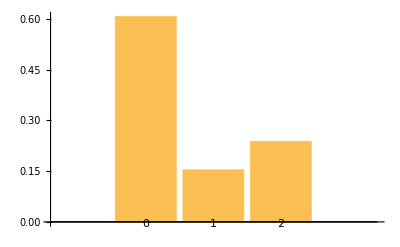

```mathematica
QuantumMeasurementOperator[QuantumBasis[3]][QuantumState["RandomPure",{3}]]["ProbabilityPlot"]
```

Plot measurement probabilities for measuring a qubit in Pauli-X basis:

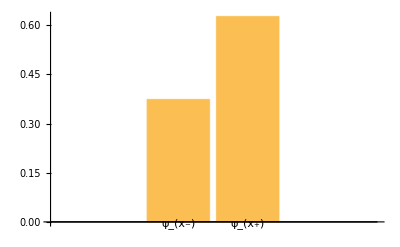

```mathematica
QuantumMeasurementOperator["X"][QuantumState["RandomPure"]]["ProbabilityPlot"]
```

Plot measurement probabilities for measuring a 2x3 composite system in computational basis:

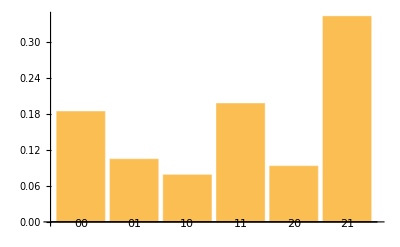

```mathematica
QuantumMeasurementOperator[QuantumBasis[{2,3}]][QuantumState["RandomPure",{2,3}]]["ProbabilityPlot"]
```

Define a random pure state for 2-qubits:

```mathematica
ψ=QuantumState[{"RandomPure",2}]
```

QuantumState[…]

Find measurement results, with and without a bit-flip noise channel with the probability 0.3:

```mathematica
m1=QuantumMeasurementOperator[{1,2}][ψ];
m2=QuantumMeasurementOperator[{1,2}][QuantumChannel[{"BitFlip",.3}][ψ]];
```

Compare measurement results:

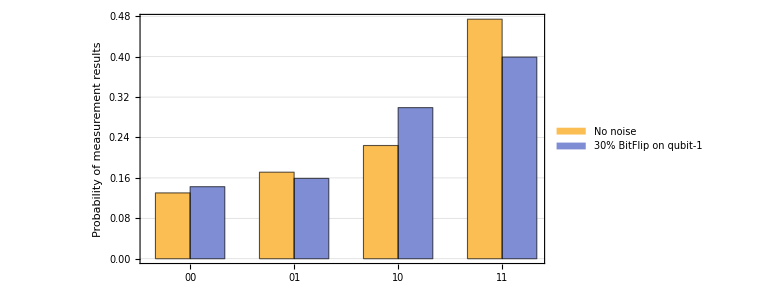

```mathematica
BarChart[Transpose[Values/@{m1["Probabilities"],m2["Probabilities"]}],ChartLabels->{Keys[m1["Probabilities"]],None},BarSpacing->{0,1},ChartLegends->{"No noise","30% BitFlip on qubit-1"},GridLines->Automatic,AspectRatio->1/2,ImageSize->Large,Frame->True,FrameLabel->"Probability of measurement results"]
```

## Supporting Data and Definitions

(Your data can be Dataset[…], EntityStore[…], Image[…], Audio[…] or any other expression)

```mathematica
ResourceData[{{}},"NameOfContent"]=xxxx
```

(xxxx can be your data, or File[…], CloudObject[…] or LocalObject[…] that contains it.)

## Thumbnail Image

## Source & Additional Information

### Contributed By

Wolfram Research, Quantum Computation Framework Team

### Keywords

Quantum measurement

Quantum channel

### Categories

Algebra
 Calculus
 Complex Systems
 Control Systems
 Engineering
 Food & Nutrition
 Graphs & Networks
 Machine Learning
 Optimization
 Puzzles and Recreation
 System Modeling
 Video Processing
  |  Astronomy
 Cellular Automata
 Computer Science
 Creative Arts
 Finance & Economics
 Geography
 Image Processing
 Mathematics
 Physics
 Signal Processing
 Text & Language Processing
 Visualization & Graphics
 |  Audio Processing
 Chemistry
 Computer Vision
 Data Science
 Finite Element Method
 Geometry
 Life Sciences
 Notebooks & User Interfaces
 Presentation & Publication
 Social Sciences
 Time-Related Computation
 Quantum Computation

### Related Documentation Pages

Symbol name or documentation URI

### Related Resource Objects

Resource Name (resources from any Wolfram repository)

### Original Source References and Attributions

Source, reference or citation

### Links

https://resources.wolframcloud.com/PacletRepository/resources/Wolfram/QuantumFramework/

### Compatibility

#### Wolfram Language Version

13.2+

#### Operating System

Windows |  Mac |  Linux

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

## Author Notes

Additional information about limitations, issues, etc.